## Bose-Hubbard model simulation

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Bose-Hubbard Hamiltonian

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
HBose[t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
HBose[t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]],{j,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(j-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j)]],{j,1,L}]
```

### Simulation parameters

```mathematica
(* kinetic hopping parameter *)
Subscript[tH, val]=1;
```

```mathematica
(* interaction strength *)
Subscript[U, val]=5;
```

```mathematica
(* chemical potential *)
Subscript[μ, val]=1/7;
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
(* inverse temperatures *)
Subscript[β, list]=Range[0,3/5,1/40];
Length[%]
```

25

### Imaginary time evolution of density and energy

#### Read simulation results from disk

```mathematica
Subscript[fn, import]="../output/bose_hubbard/L"<>ToString[Subscript[L, val]]<>"_imag_time/bose_hubbard_L"<>ToString[Subscript[L, val]]<>"_M"<>ToString[Subscript[M, val]];
```

```mathematica
Subscript[density, evolve]=Partition[Import[Subscript[fn, import]<>"_density.dat","Real64"],Subscript[L, val]];
Dimensions[%]
```

{25,5}

```mathematica
(* example *)
Subscript[density, evolve]⟦{1,2,-1}⟧
```

{{1.,1.,1.,1.,1.},{0.96168,0.961798,0.961802,0.961804,0.961686},{0.621552,0.675377,0.67607,0.675414,0.621585}}

```mathematica
Subscript[energy, evolve]=Import[Subscript[fn, import]<>"_energy.dat","Real64"]
Dimensions[%]
```

{7.61905,6.79604,6.00529,5.25309,4.54407,3.88126,3.26611,2.69873,2.17813,1.70245,1.26924,0.875637,0.518602,0.195019,-0.0981746,-0.363915,-0.604964,-0.823944,-1.02312,-1.20462,-1.37034,-1.52199,-1.66108,-1.78896,-1.90681}

{25}

#### Reference calculation

```mathematica
OperatorAverage[A_,H_,β_]:=Module[{expβH=MatrixExp[-β H]},Tr[expβH.A]/Tr[expβH]]
```

```mathematica
SiteNumberOpFull[j_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^j],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-j-1)]]
```

```mathematica
(* density *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],HB},HB=N[HBose[tH,U,μ,M,L]];Subscript[density, evolve,ref]=Table[OperatorAverage[SiteNumberOpFull[i,M,L],HB,β],{β,Subscript[β, list]},{i,0,L-1}]];
Dimensions[%]
```

{25,5}

```mathematica
(* compare *)
Max[Norm/@(Subscript[density, evolve]-Subscript[density, evolve,ref])]
```

0.0000802286

```mathematica
(* energy *)
Block[{tH=Subscript[tH, val],U=Subscript[U, val],μ=Subscript[μ, val],M=Subscript[M, val],L=Subscript[L, val],HB},HB=N[HBose[tH,U,μ,M,L]];Subscript[energy, evolve,ref]=Table[OperatorAverage[HB,HB,β],{β,Subscript[β, list]}]];
Dimensions[%]
```

{25}

```mathematica
(* compare *)
Norm[Subscript[energy, evolve]-Subscript[energy, evolve,ref],∞]
```

0.000162947

#### Visualize results

```mathematica
Subscript[plot, label]="Bose-Hubbard model with\nt_H="<>ToString[Subscript[tH, val]]<>", U="<>ToString[Subscript[U, val]]<>", μ="<>ToString[InputForm[Subscript[μ, val]]]<>", M="<>ToString[Subscript[M, val]]<>", L="<>ToString[Subscript[L, val]];
```

```mathematica
Subscript[fn, export]="plots/"<>#<>"/"<>#<>"_"&[FileBaseName[NotebookFileName[]]];
```

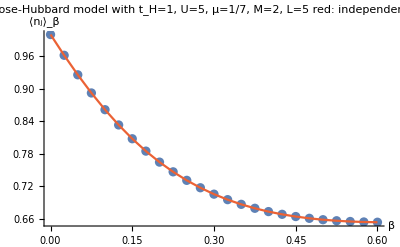

```mathematica
ListPlot[{Transpose[{Subscript[β, list],Mean/@Subscript[density, evolve]}],Transpose[{Subscript[β, list],Mean/@Subscript[density, evolve,ref]}]},AxesLabel->{"β","⟨n_j⟩_β"},Joined->{False,True},PlotStyle->{ColorData[97][1],ColorData[97][4]},PlotLabel->"average density\n"<>Subscript[plot, label]<>"\nred: independent reference calculation"]
Export[Subscript[fn, export]<>"density.pdf",%];
```

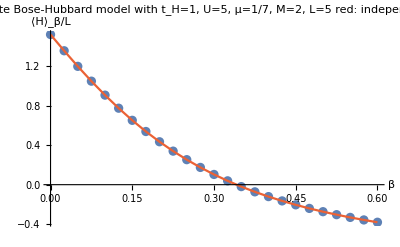

```mathematica
ListPlot[{Transpose[{Subscript[β, list],Subscript[energy, evolve]/Subscript[L, val]}],Transpose[{Subscript[β, list],Subscript[energy, evolve,ref]/Subscript[L, val]}]},AxesLabel->{"β","⟨H⟩_β/L"},Joined->{False,True},PlotStyle->{ColorData[97][1],ColorData[97][4]},PlotLabel->"average energy per site\n"<>Subscript[plot, label]<>"\nred: independent reference calculation"]
Export[Subscript[fn, export]<>"energy.pdf",%];
```

### Virtual bond dimensions

```mathematica
Subscript[D, evolve]=Partition[Import[Subscript[fn, import]<>"_D.dat","Integer64"],Subscript[L, val]+1];
Dimensions[%]
```

{25,6}

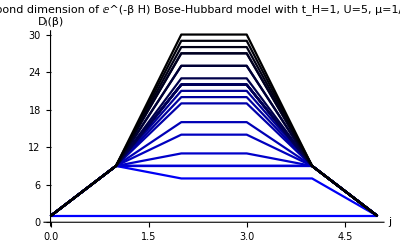

```mathematica
ListLinePlot[Transpose[{Range[0,Subscript[L, val]],#}]&/@Subscript[D, evolve],AxesLabel->{"j","D_j(β)"},PlotRange->All,PlotLabel->"virtual bond dimension of ⅇ^(-β H)\n"<>Subscript[plot, label],PlotStyle->Table[Darker[Blue,i/(Length[Subscript[β, list]]-1)],{i,0,Length[Subscript[β, list]]-1}](*,PlotLegends->("t="<>ToString[InputForm[#]]&/@Subscript[t, plot])*)]
Export[Subscript[fn, export]<>"D.pdf",%];
```

### Effective truncation weight

```mathematica
(* tolerance (truncation weight) for ⅇ^(-β H) *)
Norm[Partition[Import[Subscript[fn, import]<>"_tol_eff.dat","Real64"],Subscript[L, val]-1]-10^-10]
```

0.